# FourierShiftInverse

Inverse zero-frequency shift

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
FourierShiftInverse[data_?ArrayQ]:=FourierShiftInverse[data,All]
FourierShiftInverse[data_?ArrayQ,dim_]:=Block[
  {n=ConstantArray[0,ArrayDepth@data]},
  n[[dim]]=Check[
      Ceiling[Dimensions[data]/2][[dim]],
      Return[data,Block]
  ];
  RotateRight[data,n]
]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

FourierShiftInverse[data]

rearranges a zero-frequency-shifted Fourier transform data back to the original transform output.

FourierShiftInverse[data, dim]

operates along the dimension dim of data.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

ResourceFunction["FourierShiftInverse"] is the inverse of ResourceFunction["FourierShift"].

In optics, the zero frequency term appears in the center of spectrum.

Typically work with InverseFourier.

InverseFourier assumes that the zero frequency term appears at position 1 in the input list.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Swap the left and right halves of a vector:

```mathematica
FourierShiftInverse[{1,2,3,4,5,6}]
```

{4,5,6,1,2,3}

If a vector has an odd number of elements, then the middle element is considered part of the right half of the vector:

```mathematica
FourierShiftInverse[{1,2,3,4,5,6,7}]
```

{4,5,6,7,1,2,3}

Swap the first quadrant of the matrix with the third, and the second quadrant with the fourth:

```mathematica
FourierShiftInverse[({{1, 2, 3, 4}, {5, 6, 7, 8}, {9, 10, 11, 12}})]//MatrixForm
```

(7 | 8 | 5 | 6
11 | 12 | 9 | 10
3 | 4 | 1 | 2)

Swap halves of each column of matrix:

```mathematica
FourierShiftInverse[({{1, 2, 3, 4}, {5, 6, 7, 8}, {9, 10, 11, 12}}),1]//MatrixForm
```

(5 | 6 | 7 | 8
9 | 10 | 11 | 12
1 | 2 | 3 | 4)

Swap halves of each column of matrix:

```mathematica
FourierShiftInverse[({{1, 2, 3, 4}, {5, 6, 7, 8}, {9, 10, 11, 12}}),2]//MatrixForm
```

(3 | 4 | 1 | 2
7 | 8 | 5 | 6
11 | 12 | 9 | 10)

### Scope

Can be applied to a multidimensional array:

```mathematica
FourierShiftInverse[({{({{1, 2}, {3, 4}, {5, 6}}), ({{7, 8}, {9, 10}, {11, 12}})}, {({{13, 14}, {15, 16}, {17, 18}}), ({{19, 20}, {21, 22}, {23, 24}})}})]//MatrixForm
```

((22 | 21
24 | 23
20 | 19) | (16 | 15
18 | 17
14 | 13)
(10 | 9
12 | 11
8 | 7) | (4 | 3
6 | 5
2 | 1))

Dimension can be any valid part specification:

```mathematica
FourierShiftInverse[({{({{1, 2}, {3, 4}, {5, 6}}), ({{7, 8}, {9, 10}, {11, 12}})}, {({{13, 14}, {15, 16}, {17, 18}}), ({{19, 20}, {21, 22}, {23, 24}})}}),-2;;]//MatrixForm
```

((4 | 3
6 | 5
2 | 1) | (10 | 9
12 | 11
8 | 7)
(16 | 15
18 | 17
14 | 13) | (22 | 21
24 | 23
20 | 19))

```mathematica
FourierShiftInverse[({{({{1, 2}, {3, 4}, {5, 6}}), ({{7, 8}, {9, 10}, {11, 12}})}, {({{13, 14}, {15, 16}, {17, 18}}), ({{19, 20}, {21, 22}, {23, 24}})}}),{1,-1}]//MatrixForm
```

((14 | 13
16 | 15
18 | 17) | (20 | 19
22 | 21
24 | 23)
(2 | 1
4 | 3
6 | 5) | (8 | 7
10 | 9
12 | 11))

### Applications

An optical low-pass filter model:

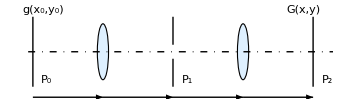
-Graphics-"4f filter system"

```mathematica
opticalLowpass[data_,r_]:=InverseFourier[Fourier@data*FourierShiftInverse@DiskMatrix[r,Dimensions@data]]
opticalLowpass[image_Image,r_]:=Image@Abs@opticalLowpass[ImageData@image,r]
```

Apply to a image:

```mathematica
opticalLowpass[-Graphics-,32]
```

-Graphics-

### Properties and Relations

ResourceFunction["FourierShiftInverse"] is the inverse of ResourceFunction["FourierShift"]:

```mathematica
FourierShiftInverse@{{"[◼]", "FourierShift"}}[{1,2,3,4,5,6,7}]
```

{1,2,3,4,5,6,7}

### Possible Issues

Only support full arrays:

```mathematica
FourierShiftInverse[{1,{2},3}]
```

FourierShiftInverse[{1,{2},3}]

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Yong-an Lu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Fourier transform

rearrange

optics

data processing

### Categories

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

InverseFourier

RotateRight

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

FourierShift

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

MATLAB ifftshift

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
FourierShiftInverse[{1,2,3,4,5,6,7}]
```

{4,5,6,7,1,2,3}

```mathematica
FourierShiftInverse[{{1,2,3,4},{5,6,7,8},{9,10,11,12}}]
```

{{7,8,5,6},{11,12,9,10},{3,4,1,2}}

```mathematica
FourierShiftInverse[{{1,2,3,4},{5,6,7,8},{9,10,11,12}},2]
```

{{3,4,1,2},{7,8,5,6},{11,12,9,10}}

```mathematica
FourierShiftInverse[{{{{1,2},{3,4},{5,6}},{{7,8},{9,10},{11,12}}},
  {{{13,14},{15,16},{17,18}},{{19,20},{21,22},{23,24}}}},-2;;]
```

{{{{4,3},{6,5},{2,1}},{{10,9},{12,11},{8,7}}},{{{16,15},{18,17},{14,13}},{{22,21},{24,23},{20,19}}}}

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

A replica of ifftshift in MATLAB.

This is nice but the name is misleading-- it suggests a shift of InverseFourier. An appropriate name would be, for example, FourierShiftInverse or FourierShiftInvert.

According to the code review comments, I modified the function name: InverseFourierShift → FourierShiftInverse.